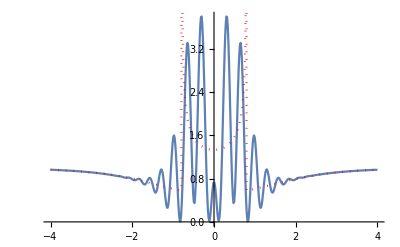

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=(x-μ)^2/2+2/(1+x^2)
ξ[x_]=μ/.Solve[f'[x]==0,μ]⟦1⟧;
ν=10;
data=√(ν/(2π ⅈ))Partition[BinaryReadList["result.bin","Real64"],2].{1,ⅈ};
Show[
ListLinePlot[Abs[data]^2,PlotRange->All,DataRange->{-4,4},PlotRange->{{-4,4},{0,4}}],
Plot[Total[1/Abs[ξ'[x]]/.NSolve[ξ[x]==μ,x,Reals]],{μ,-4,4},PlotStyle->{Red,Dotted},PlotRange->{{-4,4},{0,4}}]
]
```